## Data

```mathematica
(*files=FileNames["psl*.nc"];
<<JLink`;
InstallJava[];
ReinstallJava[JVMArguments -> "-Xmx460108m"];
testpoint[poly_, pt_] := Round[(Total@ Mod[(# - RotateRight[#]) &@(ArcTan @@ (pt - #) & /@ poly), 2 Pi, -Pi]/2/Pi)] != 0
position=Block[{extend,nlat,nlon,olat,olon},
        extend=4;
        {nlat,nlon}=Import[FileNames["psl*"][[1]],{"Datasets",{"lat","lon"}}];
        {olat,olon}=Block[{tempt=Import["P.mx"]},{tempt["lat"],tempt["lon"]}];
        {{Position[nlat,olat[[1]]][[1,1]]-extend,Position[nlat,olat[[-1]]][[1,1]]+extend+1},
         {Position[nlon,olon[[1]]][[1,1]]-extend,Position[nlon,olon[[-1]]][[1,1]]+extend}}];
data=Map[Import[#,{"Datasets","/psl"}][[;;,position[[1,1]];;position[[1,2]],position[[2,1]];;position[[2,2]]]]&,FileNames["psl*nc"]];
data=Flatten[data,1];
{nlat,nlon}=Block[{nlat,nlon},
        {nlat,nlon}=Import[FileNames["psl*nc"][[1]],{"Datasets",{"lat","lon"}}];
        {nlat[[position[[1,1]];;position[[1,2]]]],
         nlon[[position[[2,1]];;position[[2,2]]]]}];
Export["psl.mx",<|"data"->data,"lat"->nlat,"lon"->nlon|>];*)
```

```mathematica
{nP4Obser,ndynamics4Obser,position,validMatrix,plat4Obser,plon4Obser,dlat4Obser,dlon4Obser}=
	Block[{P,dynamics,position,ndynamics,validMatrix,nP,plat,plon,dlat,dlon},
        SetDirectory["/Users/pan11/Documents/CycleGAN/Data/Observation/"];
        P=Import["P.mx"]["data"];
        dynamics=Block[{hus,zg,slp},
                hus=Block[{tempt=Import["hus.mx"]["data"]},Table[Mean[tempt[[i*8+1;;(i+1)*8]]],{i,0,Length[tempt]/8-1}]];
                zg=Block[{tempt=Import["zg.mx"]["data"]},Table[Mean[tempt[[i*8+1;;(i+1)*8]]],{i,0,Length[tempt]/8-1}]];
                slp=Block[{tempt=Import["slp.mx"]["data"]},Table[Mean[tempt[[i*8+1;;(i+1)*8]]],{i,0,Length[tempt]/8-1}]];
                Transpose[{slp,zg,hus}]];
        position=Block[{valiMatrix,mP},
                valiMatrix=Block[{tempt=P[[1]]},Table[If[tempt[[i,j]]<0,0,1],{i,100},{j,236}]];
                mP=Table[Mean[Flatten[P[[i]]*valiMatrix]],{i,Length[P]}];
                Position[mP,_?(#>=0.&)][[;;,1]]];
        ndynamics=Block[{tempt=dynamics[[position]]},
                Transpose[Table[Block[{mean,sigma},
                                mean=Mean[tempt[[;;,i]]];
                                sigma=Sqrt[Variance[tempt[[;;,i]]]];
                        Map[(#-mean)/sigma&,tempt[[;;,i]]]],{i,Dimensions[tempt][[2]]}]]];
        validMatrix=Block[{tempt1=ArrayResample[P[[1]],{27,48},"Bin"]},
                Table[If[tempt1[[i,j]]<0,0,1],{i,Length[tempt1]},{j,Dimensions[tempt1][[2]]}]];
        nP=Block[{tempt},
                tempt=Map[ArrayResample[#,{27,48},"Bin"]*validMatrix&,P[[position]]];
                Log[tempt+1.]];
        plat=Import["P.mx"]["lat"];
		plon=Import["P.mx"]["lon"];
		dlat=Import["hus.mx"]["lat"];
		dlon=Import["hus.mx"]["lon"];
        {nP,ndynamics,position,validMatrix,plat,plon,dlat,dlon}];
```

```mathematica
{nP4GCM,ndynamics4GCM,plat4GCM,plon4GCM,dlat4GCM,dlon4GCM}=Block[{dir,p,np,dynamics,ndynamics,nP,plat,plon,dlat,dlon},
        dir="/Users/pan11/Documents/CycleGAN/Data/CESM/";
        SetDirectory[dir];
        p=Import["P.mx"]["data"];
        dynamics=Block[{hus,zg,psl},
                hus=Import["hus.mx"]["data"];
                zg=Import["zg.mx"]["data"];
                psl=Import["psl.mx"]["data"];
                Transpose[{psl,zg[[;;,2]],hus[[;;,2]]}]];
        ndynamics=Transpose[Table[Block[{mean,sigma},
                mean=Mean[dynamics[[;;,i]]];
                sigma=Sqrt[Variance[dynamics[[;;,i]]]];
                Map[(#-mean)/sigma&,dynamics[[;;,i]]]],{i,Dimensions[dynamics][[2]]}]];
        nP=Map[#*validMatrix&,Log[p*24*3600+1.]];
        plat=Import["P.mx"]["lat"];
		plon=Import["P.mx"]["lon"];
		dlat=Import["hus.mx"]["lat"];
		dlon=Import["hus.mx"]["lon"];
        {nP, ndynamics,plat,plon,dlat,dlon}];
```

```mathematica
nP4Obser=nP4Obser[[;;,1;;26]];
plat4Obser=plat4Obser[[1;;26]];
validMatrix=validMatrix[[1;;26]];
nP4GCM=nP4GCM[[position,1;;26]];
ndynamics4GCM=ndynamics4GCM[[position]];
plat4GCM=plat4GCM[[1;;26]];
nP4GCM=Map[List,nP4GCM];
nP4Obser=Map[List,nP4Obser];
```

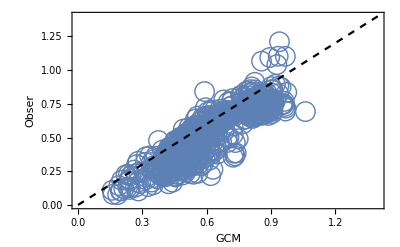

```mathematica
Show[{ListPlot[DeleteCases[Transpose[{Flatten[Mean[nP4GCM]],Flatten[Mean[nP4Obser]]}],{0.,0.}],
 PlotRange->{{0,1.4},{0,1.4}},PlotMarkers->Style["○",20],
 Frame->True,FrameLabel->{"GCM","Obser"},BaseStyle->{FontFamily->"Arial",15},
 ImageSize->400],
 Plot[x,{x,0.,1.4},PlotStyle->{Black,Dashed}]}]
```

```mathematica
color[x_]:=Rcolorfunction[x,.01,1.]
plot[Mean[nP4GCM][[1]],plat4GCM,plon4GCM]
plot[Mean[nP4Obser][[1]],plat4GCM,plon4GCM]
```

```mathematica
day=RandomSample[Range[Length[nP4Obser]]][[1]];
color[x_]:=Rcolorfunction[x,0.001,3]
a1=plot[nP4GCM[[day,1]],plat4GCM,plon4GCM];
a2=plot[nP4Obser[[day,1]],plat4GCM,plon4GCM];
color[x_]:=Rcolorfunction[x,-2.,2.]
b1=Table[plot[ndynamics4GCM[[day,i]],dlat4GCM,dlon4GCM],{i,3}];
b2=Table[plot[ndynamics4Obser[[day,i]],dlat4GCM,dlon4GCM],{i,3}];

Framed[Style[TableForm[Transpose[{Prepend[b1,a1],Prepend[b2,a2]}],TableSpacing->{0, 0},
TableHeadings->{Map[Rotate[#,Pi/2]&,{"P","SLP","Z_500","SH_500"}],{"CanESM_historical","Obser/Reanalysis"}},
TableAlignments->Center],{FontFamily->"Arial",20}]]
```

## Model_usingNetGanOperator

```mathematica
discriminator=NetChain[{ConvolutionLayer[16,{3,3}],
						BatchNormalizationLayer[],
						Ramp,
						ConvolutionLayer[32,{3,3}],
						BatchNormalizationLayer[],
						Ramp,
						PoolingLayer[2,2],
						ConvolutionLayer[64,{3,3}],
						BatchNormalizationLayer[],
						Ramp,
						ConvolutionLayer[64,{3,3}],
						BatchNormalizationLayer[],
						Ramp,
						PoolingLayer[2,2],
						FlattenLayer[],
						BatchNormalizationLayer[],
						LinearLayer[500],
						Ramp,
						LinearLayer[{}],
						ElementwiseLayer[LogisticSigmoid]},
		"Input"->{1,27,48},
		"Output" -> NetDecoder["Boolean"]]
```

```mathematica
generator=NetChain[{ConvolutionLayer[32,5,"PaddingSize"->2],
					BatchNormalizationLayer[],
					Ramp,
					ConvolutionLayer[64,5,"PaddingSize"->2],
					BatchNormalizationLayer[],
					Ramp,
					ConvolutionLayer[128,5,"PaddingSize"->2],
					BatchNormalizationLayer[],
					Ramp,
					PoolingLayer[2,2],
					DeconvolutionLayer[64, 4, "Stride" -> 2],
					BatchNormalizationLayer[],
					Ramp,
					ConvolutionLayer[1,1],
					BatchNormalizationLayer[],
					Ramp,
					PartLayer[{;;,1;;-2,2;;-2}],
					ConstantTimesLayer["Scaling" -> {validMatrix},"LearningRateMultipliers"->0]},
					"Input" -> NetExtract[discriminator, "Input"]]
```

```mathematica
generatorGCM2Obser = NetInsertSharedArrays[generator, "Generator_GCM2Obser/"];
ganGCM2Obser = NetGANOperator[{generatorGCM2Obser, discriminator}];
generatorObser2GCM = NetInsertSharedArrays[generator, "Generator_Obser2GCM/"];
ganObser2GCM = NetGANOperator[{generatorObser2GCM, discriminator}];
cycleGAN = NetGraph[<|"GAN_GCM2Obser" -> ganGCM2Obser, "GAN_Obser2GCM" -> ganObser2GCM, 
   "Generator_GCM2Obser" -> generatorGCM2Obser , "Generator_Obser2GCM" -> generatorObser2GCM,
   "ME_GCM2Obser" -> MeanAbsoluteLossLayer[], 
   "ME_Obser2GCM" -> MeanAbsoluteLossLayer[]|>, 
  {NetPort["Obser"] -> {NetPort["GAN_GCM2Obser", "Sample"], NetPort["GAN_Obser2GCM", "Latent"]}, 
   NetPort["GCM"] -> {NetPort["GAN_Obser2GCM", "Sample"], NetPort["GAN_GCM2Obser", "Latent"]}, 
   NetPort["GAN_GCM2Obser", "GeneratedFake"] -> "Generator_Obser2GCM" -> "ME_GCM2Obser" -> NetPort["LossCycle_GCM2Obser"], 
   NetPort["GCM"] -> NetPort["ME_GCM2Obser", "Target"], 
   NetPort["GAN_Obser2GCM", "GeneratedFake"] -> "Generator_GCM2Obser" -> "ME_Obser2GCM" -> NetPort["LossCycle_Obser2GCM"], 
   NetPort["Obser"] -> NetPort["ME_Obser2GCM", "Target"]}]
```

```mathematica
GCM=Map[List,nP4GCM];
Obser=Map[List,nP4Obser];
```

```mathematica
showCycleGan[net_] := 
  Block[{generatorGCM2Obser, generatorObser2GCM, 
         generatedGCM2Obser, generatedObser2GCM,
         reconstructedGCM2Obser,reconstructedObser2GCM, 
         GCMSamples,ObserSamples,
         decoder}, 
   decoder=NetDecoder["Image"];
   GCMSamples=RandomSample[GCM,10];
   ObserSamples=RandomSample[Obser,10];
   generatorGCM2Obser = net[["Generator_GCM2Obser"]];
   generatorObser2GCM  = net[["Generator_Obser2GCM"]];
   generatedGCM2Obser = generatorGCM2Obser[GCMSamples]; 
   reconstructedGCM2Obser = generatorObser2GCM[generatedGCM2Obser]; 
   generatedObser2GCM = generatorObser2GCM[ObserSamples]; 
   reconstructedObser2GCM = generatorGCM2Obser[generatedObser2GCM]; 
   Grid[MapThread[
   Prepend, {Map[decoder,{GCMSamples, reconstructedGCM2Obser, generatedGCM2Obser, 
                          ObserSamples, reconstructedObser2GCM, generatedObser2GCM}], 
        {"GCM", "GCM_Reconstruct", "Obser_Generated", 
        "Obser", "Obser_Reconstruct", "GCM_Generated"} // 
       Map[Style[#, "Text"] &]}], 
    Sequence[Alignment -> {Right, Center}, 
     Frame -> {Prepend[Table[True, 10], False], {False, False, False, 
        True, False, False}}]]];
```

```mathematica
cycleGAN=Import["/Users/pan11/trained.mx"];
```

```mathematica
trained = 
 NetTrain[cycleGAN, {Function[<|
     "GCM" -> RandomSample[GCM, #BatchSize], 
     "Obser" -> RandomSample[Obser, #BatchSize]|>], 
   "RoundLength" -> Length[GCM]}, 
  TrainingUpdateSchedule -> {{"GAN_GCM2Obser", "Discriminator"} | {"GAN_Obser2GCM", "Discriminator"}, 
                             "Generator_GCM2Obser" | "Generator_Obser2GCM"}, 
  TrainingProgressReporting -> {{Function@showCycleGan[#Net], 
     "Interval" -> Quantity[10, "Seconds"]}, "Panel"}, 
  MaxTrainingRounds -> 125]
```

$Aborted

```mathematica
(*trained = 
 NetTrain[cycleGAN, {Function[<|
     "GCM" -> RandomSample[GCM, #BatchSize], 
     "Obser" -> RandomSample[Obser, #BatchSize]|>], 
   "RoundLength" -> Length[GCM]}, 
  TrainingUpdateSchedule -> {{"GAN_GCM2Obser", "Discriminator"} | {"GAN_Obser2GCM", 
      "Discriminator"}, "Generator_GCM2Obser" | "Generator_Obser2GCM"}, 
  MaxTrainingRounds -> 125, TargetDevice -> "GPU"]
  
simuObser=Block[{tempt=trained[["Generator_GCM2Obser"]]},
	Map[tempt[#,TargetDevice->"GPU"]&,GCM]];*)
```

```mathematica
Normal[NetExtract[trained[["Generator_Obser2GCM"]][[18]],"Scaling"][[1]]][[1]]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
showCycleGan[Import["/Users/pan11/trained.mx"]]
```

```mathematica
trained=Import["/Users/pan11/trained.mx"]
```

NetGraph[<>]

```mathematica
simuObser=Block[{tempt=trained[["Generator_GCM2Obser"]]},Map[tempt,GCM]];
```

```mathematica
MinMax[simuObser]
```

{0.,9.35234}

```mathematica
Correlation[Flatten[Mean[GCM][[1]]],Flatten[Mean[Obser][[1]]]]
Correlation[Flatten[Mean[simuObser][[1]]],Flatten[Mean[Obser][[1]]]]
```

0.972156

0.878891

```mathematica
Dimensions[Mean[GCM]]
```

{1,27,48}

```mathematica
color[x_]:=Rcolorfunction[x,0.01,1.2];
plot[Mean[GCM][[1]],plat4GCM,plon4GCM]
plot[Mean[simuObser][[1]],plat4GCM,plon4GCM]
plot[Mean[Obser][[1]],plat4GCM,plon4GCM]
```

```mathematica
color[x_]:=Rcolorfunction[x,0.1,3];
day=RandomSample[Range[Length[simuObser]]][[1]];
plot[simuObser[[day,1]],plat4GCM,plon4GCM]
plot[GCM[[day,1]],plat4GCM,plon4GCM]
```

```mathematica
Table[
SmoothHistogram[{Select[GCM[[;;,1,point[[1]],point[[2]]]],Positive],
				 Select[Obser[[;;,1,point[[1]],point[[2]]]],Positive],
	             Select[simuObser[[;;,1,point[[1]],point[[2]]]],Positive]},
	      PlotRange->Full,PlotStyle->{Red,Blue,Green},
	      Frame->True,ImageSize->100],{point,Position[validMatrix,1][[1;;-1;;10]]}]
```

```mathematica
MinMax[GCM]
MinMax[Obser]
MinMax[simuObser]
```

{0.,5.67989}

{0.,5.93982}

{0.,9.35234}

## Model_Not_Using_NetGanOperator

```mathematica
Map[Dimensions,{nP4Obser,ndynamics4Obser,position,validMatrix,plat4Obser,plon4Obser,dlat4Obser,dlon4Obser}]
Map[Dimensions,{nP4GCM,ndynamics4GCM,plat4GCM,plon4GCM,dlat4GCM,dlon4GCM}]
```

{{20794,1,26,48},{20794,3,36,56},{20794},{26,48},{26},{236},{36},{36}}

{{20794,1,26,48},{20794,3,36,56},{26},{48},{36},{56}}

```mathematica
dim={1,26,48};
dim2={3,36,56};
```

```mathematica
convolutionBlock[args___] :=
  NetChain[{ConvolutionLayer[args], NormalizationLayer[],
    ElementwiseLayer["SELU"]}];
deconvolutionBlock[args___] :=
  NetChain[{DeconvolutionLayer[args],
    PartLayer[{All, 4 ;; -4, 4 ;; -4}], NormalizationLayer[],
    Ramp}]; 
    
generator = NetGraph[<|"chain"->{
   convolutionBlock[32, 7, "PaddingSize" -> 3],
   convolutionBlock[64, 4, "PaddingSize" -> 1, "Stride" -> 2],
   convolutionBlock[128, 3, "PaddingSize" -> 1, "Stride" -> 1],
   convolutionBlock[128, 3, "PaddingSize" -> 2, "Stride" -> 1],
   deconvolutionBlock[128, 4, "Stride" -> 2],
   ConvolutionLayer[128,3,"PaddingSize"->1],
   ConvolutionLayer[1, 7, "PaddingSize" -> 3]},
   "combine"->ThreadingLayer[Plus],
   "cut"->{ConstantTimesLayer["Scaling"->{validMatrix},LearningRateMultipliers->0.],Ramp}|>,
   {NetPort["Input"]->"chain"->"combine",NetPort["Input"]->"combine"->"cut"},
   "Input"->dim];
```

```mathematica
generator=NetGraph[<|"chain"->{PaddingLayer[{{0,0},{3,3},{3,3}}],
          ConvolutionLayer[64,{3,3}],
          BatchNormalizationLayer[],
          Ramp,
          ConvolutionLayer[128,{3,3}],
          BatchNormalizationLayer[],
          Ramp,
          ConvolutionLayer[256,{3,3}],
          BatchNormalizationLayer[],
          Ramp,
          ConvolutionLayer[1,{1,1}]},
          "combine"->ThreadingLayer[Plus],
   "cut"->{ConstantTimesLayer["Scaling"->{validMatrix/2.},LearningRateMultipliers->0.],Ramp}|>,
    {NetPort["Input"]->"chain"->"combine",NetPort["Input"]->"combine"->"cut"},
     "Input"->dim]
```

NetGraph[<>]

```mathematica
Import["/g/g92/pan11/CycleGAN/2020_10_14_CycleGan_Model.m"];
Import["/g/g92/pan11/CycleGAN/2020_10_15_CycleGan_Train.m"];
```

```mathematica
generatorGCM2Obser = NetInsertSharedArrays[generator, "generatorGCM2Obser/"];
cygleGCM2Obser = NetInsertSharedArrays[generator, "generatorGCM2Obser/"];

generatorObser2GCM = NetInsertSharedArrays[generator, "generatorObser2GCM/"];
cycleObser2GCM = NetInsertSharedArrays[generator, "generatorObser2GCM/"];

discriminator = NetChain[{
	ConvolutionLayer[16,{3,3},"Stride"->1],BatchNormalizationLayer[], Ramp,
    ConvolutionLayer[32,{3,3},"Stride"->2],BatchNormalizationLayer[],Ramp,
    ConvolutionLayer[64,{3,3},"Stride"->1],BatchNormalizationLayer[],Ramp,
    ConvolutionLayer[128,{3,3},"Stride"->2],BatchNormalizationLayer[],Ramp,
    FlattenLayer[],BatchNormalizationLayer[],300,Ramp,BatchNormalizationLayer[], 1, ElementwiseLayer["HardSigmoid"]},
  "Input" -> dim];
 
discriminatorGCM2Obser = discriminator;
discriminatorObser2GCM = discriminator;
```

```mathematica
downscaling=Block[{contract,expand},
	contract[channel_,crop_:{{1,1},{1,1}}]:=NetGraph[{"conv"->{ConvolutionLayer[channel,{3,3},"Stride"->1,"PaddingSize"->1],Ramp,
                                                           ConvolutionLayer[channel,{3,3},"Stride"->1,"PaddingSize"->1],Ramp},
                                   "pooling"->PoolingLayer[2,2],
                                   "cropping"->PartLayer[{;;,crop[[1,1]];;-crop[[1,-1]],crop[[2,1]];;-crop[[2,-1]]}]},
                         {NetPort["Input"]->"conv"->"pooling"->NetPort["Pooling"],"conv"->"cropping"->NetPort["Shortcut"]}];

	expand[channel_]:=NetGraph[{"deconv"->{DeconvolutionLayer[channel,{2,2},"Stride"->{2,2}],Ramp},
                                                "join"->CatenateLayer[],
                                                "conv"->{ConvolutionLayer[channel,{3,3},"Stride"->1,"PaddingSize"->1],Ramp,
                                                         ConvolutionLayer[channel,{3,3},"Stride"->1,"PaddingSize"->1],Ramp}},
                         {NetPort["Input"]->"deconv"->"join",
                          NetPort["Shortcut"]->"join"->"conv"}];
	NetInitialize[NetGraph[<|"contract_1"->contract[64,{{3,3},{5,5}}],
                   "contract_2"->contract[128,{{2,2},{3,3}}],
                   "contract_3"->contract[256,{{1,2},{2,2}}],
                   "contract_4"->contract[512,{{1,1},{1,2}}],
                   "expand_1"->expand[64],
                   "expand_2"->expand[128],
                   "expand_3"->expand[256],
                   "expand_4"->expand[512],
                   "ubase"->{ConvolutionLayer[512,{3,3},PaddingSize->{1,1}],Ramp,ConvolutionLayer[512,{3,3},
                            PaddingSize->{1,1}],Ramp,DropoutLayer[0.5]},
                   "output"->{ConvolutionLayer[1,{1,1}],Ramp,PartLayer[{;;,4;;29,;;}]},
                   "mask"->ConstantTimesLayer["Scaling"->{validMatrix},LearningRateMultipliers->0]|>,
   {NetPort["Input"]->"contract_1",
        NetPort["contract_1","Pooling"]->"contract_2",
        NetPort["contract_2","Pooling"]->"contract_3",
        NetPort["contract_3","Pooling"]->"contract_4",
        NetPort["contract_4","Pooling"]->"ubase",
        "ubase"->NetPort["expand_4","Input"],
        NetPort["contract_4","Shortcut"]->NetPort["expand_4","Shortcut"],
        NetPort["expand_4","Output"]->NetPort["expand_3","Input"],
        NetPort["contract_3","Shortcut"]->NetPort["expand_3","Shortcut"],
        NetPort["expand_3","Output"]->NetPort["expand_2","Input"],
        NetPort["contract_2","Shortcut"]->NetPort["expand_2","Shortcut"],
        NetPort["expand_2","Output"]->NetPort["expand_1","Input"],
        NetPort["contract_1","Shortcut"]->NetPort["expand_1","Shortcut"],
        NetPort["expand_1","Output"]->"output"->"mask"},
   "Input"->Dimensions[ndynamics4GCM][[2;;]]]]];
```

```mathematica
downscaleGCM = NetInsertSharedArrays[downscaling, "downscaleGCM/"];
RdownscaleGCM = NetInsertSharedArrays[downscaling, "downscaleGCM/"];

downscaleObser = NetInsertSharedArrays[downscaling, "downscaleObser/"];
RdownscaleObser = NetInsertSharedArrays[downscaling, "downscaleObser/"];
```

```mathematica
cycleGAN =
 NetInitialize[
  NetGraph[<|
    "Generator_GCM->Obser" -> generatorGCM2Obser,
    "Cycle_GCM->Obser" -> cygleGCM2Obser,
    "Discriminator_GCM->Obser" -> NetMapOperator[discriminatorGCM2Obser],
    "Cat_GCM->Obser" -> CatenateLayer[],
    "Reshape_GCM->Obser" -> ReshapeLayer[Prepend[dim,2]],
    "Flat_GCM->Obser" -> ReshapeLayer[{2}],
    "Fake_GCM->Obser"->PartLayer[1],
    "Real_GCM->Obser"->PartLayer[2],
    "Scale_GCM->Obser" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
    "MS_GCM->Obser"->MeanAbsoluteLossLayer[],
   

    "Generator_Obser->GCM" -> generatorObser2GCM,
    "Cycle_Obser->GCM" -> cycleObser2GCM,
    "Discriminator_Obser->GCM" -> NetMapOperator[discriminatorObser2GCM],
    "Cat_Obser->GCM" -> CatenateLayer[],
    "Reshape_Obser->GCM" -> ReshapeLayer[Prepend[dim,2]],
    "Flat_Obser->GCM" -> ReshapeLayer[{2}],
    "Fake_Obser->GCM"->PartLayer[1],
    "Real_Obser->GCM"->PartLayer[2],
    "Scale_Obser->GCM" -> ConstantTimesLayer["Scaling" -> {-1, 1},LearningRateMultipliers->0],
    "MS_Obser->GCM"->MeanAbsoluteLossLayer[],
    
    "Downscaling_GCM"->downscaleGCM,
    "Downscaling_Obser"->downscaleObser,
    
    "R_Downscaling_GCM"->RdownscaleGCM,
    "R_Downscaling_Obser"->RdownscaleObser,
    
    "MS_GCM_Downscaling"->MeanAbsoluteLossLayer[],
    "MS_Obser_Downscaling"->MeanAbsoluteLossLayer[],
    
    "MS_GCM_RDownscaling"->MeanAbsoluteLossLayer[],
    "MS_Obser_RDownscaling"->MeanAbsoluteLossLayer[]|>,

   {NetPort["P_GCM"] ->"Generator_GCM->Obser" ->"Cat_GCM->Obser",
    NetPort["P_Obser"] -> "Cat_GCM->Obser",
    "Cat_GCM->Obser" -> "Reshape_GCM->Obser" -> "Discriminator_GCM->Obser" -> "Flat_GCM->Obser" -> "Scale_GCM->Obser" ->
    "Fake_GCM->Obser"->NetPort["FakeLoss_GCM->Obser"],
    "Scale_GCM->Obser"->"Real_GCM->Obser"->NetPort["RealLoss_GCM->Obser"],
    "Generator_GCM->Obser"->"Cycle_Obser->GCM"->"MS_GCM->Obser",
    NetPort["P_GCM"]->"MS_GCM->Obser"->NetPort["ReconstructionLoss_GCM->Obser"],

    
    NetPort["D_GCM"]->"Downscaling_GCM"->"MS_GCM_Downscaling",
    NetPort["P_GCM"]->"MS_GCM_Downscaling"->NetPort["Loss_Downscaling_GCM"],
    NetPort["D_Obser"]->"Downscaling_Obser"->"MS_Obser_Downscaling",
    NetPort["P_Obser"]->"MS_Obser_Downscaling"->NetPort["Loss_Downscaling_Obser"],
    
    NetPort["D_GCM"]->"R_Downscaling_Obser"->"MS_Obser_RDownscaling",
    "Generator_GCM->Obser"->"MS_Obser_RDownscaling"->NetPort["Loss_RDownscaling_GCM"],
     NetPort["D_Obser"]->"R_Downscaling_GCM"->"MS_GCM_RDownscaling",
    "Generator_Obser->GCM"->"MS_GCM_RDownscaling"->NetPort["Loss_RDownscaling_Obser"],
    

    NetPort["P_Obser"] ->"Generator_Obser->GCM" -> "Cat_Obser->GCM",
    NetPort["P_GCM"] -> "Cat_Obser->GCM",
    "Cat_Obser->GCM" -> "Reshape_Obser->GCM" -> "Discriminator_Obser->GCM" -> "Flat_Obser->GCM" -> "Scale_Obser->GCM" ->
    "Fake_Obser->GCM"->NetPort["FakeLoss_Obser->GCM"],
    "Scale_Obser->GCM"->"Real_Obser->GCM"->NetPort["RealLoss_Obser->GCM"],
    "Generator_Obser->GCM"->"Cycle_GCM->Obser"->"MS_Obser->GCM",
    NetPort["P_Obser"]->"MS_Obser->GCM"->NetPort["ReconstructionLoss_Obser->GCM"]
    },
   "P_Obser" -> dim,
   "P_GCM" -> dim,
   "D_GCM" -> dim2,
   "D_Obser" -> dim2]]
```

NetGraph[<>]

## Step-by-step Training

```mathematica
length=Round[Length[nP4GCM]*0.8];
validation=Table[<|"P_GCM"->nP4GCM[[i]],"D_GCM"->ndynamics4GCM[[i]],
             "P_Obser"->nP4Obser[[i]],"D_Obser"->ndynamics4Obser[[i]]|>,{i,length,Length[nP4GCM]}];
             
DiffMean=Infinity;
DiffVar=Infinity;

GCMDownscalingLoss=Infinity;
ObserDownscalingLoss=Infinity;

obserMean=Mean[validation[[;;,"P_Obser"]]][[1]];
obserVar=Variance[validation[[;;,"P_Obser"]]][[1]];
```

```mathematica
index=CreateUUID[]
```

05fc8f6c-23fc-4c22-a352-9bb58de56a57

```mathematica
ReportCycleGan1[net_] :=
  Block[{gen,dGCM,dObser,obserG,obserD,gcmD,meanDiff,varDiff,dlossGCM,dlossObser},
        dGCM=net[["Downscaling_GCM"]];
        dObser=net[["Downscaling_Obser"]];
        
        obserD=Map[dObser[#,TargetDevice->"GPU"]&,validation[[;;,"D_Obser"]]];
        gcmD=Map[dGCM[#,TargetDevice->"GPU"]&,validation[[;;,"D_GCM"]]];
        
        dlossObser=Mean[Abs[Flatten[obserD-validation[[;;,"P_Obser"]]]]];
        dlossGCM=Mean[Abs[Flatten[gcmD-validation[[;;,"P_GCM"]]]]];
        Print[TableForm[{{DiffMean,DiffVar,GCMDownscalingLoss,ObserDownscalingLoss},
               {meanDiff,varDiff,dlossGCM,dlossObser}},TableAlignments->Center]];
        If[And[(*meanDiff<=DiffMean,varDiff<=DiffVar,*)dlossGCM<=GCMDownscalingLoss,dlossObser<=ObserDownscalingLoss],
          Block[{},
                Export["/g/g92/pan11/CycleGAN_trained_Step_1_"<>index<>".mx",net];
                Set[{GCMDownscalingLoss,ObserDownscalingLoss},
                    {dlossGCM,dlossObser}]]]];
```

```mathematica
trained1 = 
	NetTrain[cycleGAN, 
	{Function[Block[{base,choice},
	base=RandomSample[Range[length],#BatchSize];
	choice=Map[Block[{daylag=RandomSample[Range[-15,15]][[1]],yearlag=RandomSample[Range[-5,5]][[1]],tempt},
				tempt=#+daylag+yearlag*365;
				If[And[tempt>0,tempt≤length],tempt,#]]&,base];
	<|"P_GCM"->nP4GCM[[base]],
      "D_GCM"->ndynamics4GCM[[base]],
      "P_Obser"->nP4Obser[[choice]],
      "D_Obser"->ndynamics4Obser[[choice]]|>]], "RoundLength" -> Length[nP4GCM]}, 
    LossFunction ->{"FakeLoss_GCM->Obser"->Scaled[0],"RealLoss_GCM->Obser"->Scaled[0],"ReconstructionLoss_GCM->Obser"->Scaled[0],
                    "FakeLoss_Obser->GCM"->Scaled[0],"RealLoss_Obser->GCM"->Scaled[0],"ReconstructionLoss_Obser->GCM"->Scaled[0],
                    "Loss_Downscaling_GCM"->Scaled[1],"Loss_RDownscaling_GCM"->Scaled[0],
                    "Loss_Downscaling_Obser"->Scaled[1],"Loss_RDownscaling_Obser"->Scaled[0]
                    }, 
    TrainingUpdateSchedule -> {"Discriminator_GCM->Obser"|"Discriminator_Obser->GCM",
                               "Generator_GCM->Obser"|"Generator_Obser->GCM",
                               "Downscaling_GCM"|"Downscaling_Obser"},
    LearningRateMultipliers -> {"Scale_GCM->Obser" -> 0, "Scale_Obser->GCM" -> 0,
                             "Generator_GCM->Obser" -> 0,"Generator_Obser->GCM"->0,
                             "Discriminator_Obser->GCM"->0,"Discriminator_GCM->Obser"->0,
                             "Downscaling_GCM"->1,"Downscaling_Obser"->1},
    BatchSize -> 32,
    MaxTrainingRounds->100,
    TargetDevice->"GPU",
    Method -> {"ADAM", "Beta1" -> 0.5, "LearningRate" -> 10^-4,
			   "WeightClipping" -> {"Discriminator_Obser->GCM"-> 0.05,"Discriminator_GCM->Obser"->0.05}},
    TrainingProgressReporting -> {{Function@ReportCycleGan1[#Net], "Interval" -> Quantity[1, "Rounds"]},"Print"}]
```

```mathematica
ReportCycleGan2[net_] :=
  Block[{gen,dGCM,dObser,obserG,obserD,gcmD,meanDiff,varDiff,dlossGCM,dlossObser},
        gen=net[["Generator_GCM->Obser"]];
        dGCM=net[["Downscaling_GCM"]];
        dObser=net[["Downscaling_Obser"]];
        
        obserG=Map[gen[#,TargetDevice->"GPU"]&,validation[[;;,"P_GCM"]]];
        obserD=Map[dObser[#,TargetDevice->"GPU"]&,validation[[;;,"D_Obser"]]];
        gcmD=Map[dGCM[#,TargetDevice->"GPU"]&,validation[[;;,"D_GCM"]]];
        
        meanDiff=Mean[Abs[Flatten[Mean[obserG][[1]]-obserMean]]];
        varDiff=Mean[Abs[Flatten[Variance[obserG][[1]]-obserVar]]];
(*      dlossObser=Mean[Abs[Flatten[obserD-validation[[;;,"P_Obser"]]]]];
        dlossGCM=Mean[Abs[Flatten[gcmD-validation[[;;,"P_GCM"]]]]];*)
        Print[TableForm[{{DiffMean,DiffVar,GCMDownscalingLoss,ObserDownscalingLoss},
               {meanDiff,varDiff,dlossGCM,dlossObser}},TableAlignments->Center]];
        If[And[meanDiff<=DiffMean,varDiff<=DiffVar(*,dlossGCM<=GCMDownscalingLoss,dlossObser<=ObserDownscalingLoss*)],
          Block[{},
                Export["/g/g92/pan11/CycleGAN_trained_Step_2_"<>index<>".mx",net];
                Set[{DiffMean,DiffVar(*,GCMDownscalingLoss,ObserDownscalingLoss*)},
                    {meanDiff,varDiff(*,dlossGCM,dlossObser*)}]]]];
```

```mathematica
cycleGAN=Import["/g/g92/pan11/CycleGAN_trained_Step_1_"<>index<>".mx"];
```

```mathematica
trained2 = 
	NetTrain[cycleGAN, 
	{Function[Block[{base,choice},
	base=RandomSample[Range[length],#BatchSize];
	choice=Map[Block[{daylag=RandomSample[Range[-15,15]][[1]],yearlag=RandomSample[Range[-5,5]][[1]],tempt},
				tempt=#+daylag+yearlag*365;
				If[And[tempt>0,tempt≤length],tempt,#]]&,base];
	<|"P_GCM"->nP4GCM[[base]],
      "D_GCM"->ndynamics4GCM[[base]],
      "P_Obser"->nP4Obser[[choice]],
      "D_Obser"->ndynamics4Obser[[choice]]|>]], "RoundLength" -> Length[nP4GCM]}, 
    LossFunction ->{"FakeLoss_GCM->Obser"->Scaled[1],"RealLoss_GCM->Obser"->Scaled[1],"ReconstructionLoss_GCM->Obser"->Scaled[-1],
                    "FakeLoss_Obser->GCM"->Scaled[1],"RealLoss_Obser->GCM"->Scaled[1],"ReconstructionLoss_Obser->GCM"->Scaled[-1],
                    "Loss_Downscaling_GCM"->Scaled[0],"Loss_RDownscaling_GCM"->Scaled[-1],
                    "Loss_Downscaling_Obser"->Scaled[0],"Loss_RDownscaling_Obser"->Scaled[-1]
                    }, 
    TrainingUpdateSchedule -> {"Discriminator_GCM->Obser"|"Discriminator_Obser->GCM",
                               "Generator_GCM->Obser"|"Generator_Obser->GCM"},
    LearningRateMultipliers -> {"Scale_GCM->Obser" -> 0, "Scale_Obser->GCM" -> 0,
                             "Generator_GCM->Obser" -> -1,"Generator_Obser->GCM"->-1,
                             "Discriminator_Obser->GCM"->1,"Discriminator_GCM->Obser"->1,
                             "Downscaling_GCM"->0,"Downscaling_Obser"->0,
                             "R_Downscaling_GCM"->0,"R_Downscaling_Obser"->0},
    BatchSize -> 32,
    TargetDevice->"GPU",
 
    Method -> {"ADAM", "Beta1" -> 0.5, "LearningRate" -> 10^-4,
			   "WeightClipping" -> {"Discriminator_Obser->GCM"-> 0.05,"Discriminator_GCM->Obser"->0.05}},
    TrainingProgressReporting -> {{Function@ReportCycleGan2[#Net], "Interval" -> Quantity[1, "Rounds"]},"Print"}]
```

```mathematica
(*Import["/g/g92/pan11/CycleGAN/2020_10_13_CycleGAN_Data.m"];
Import["/g/g92/pan11/CycleGAN/2020_10_14_CycleGan_Model.m"];
Import["/g/g92/pan11/CycleGAN/2020_10_15_CycleGan_Train.m"];*)
```

```mathematica
ssimuObser=Block[{models},
	SetDirectory["/Users/pan11/Documents/CycleGAN/Results/Trained"];
	models=Map[Import[#][["Generator_GCM->Obser"]]&,FileNames["*Step_2*mx"]];
	Table[Block[{tempt=models[[i]]},Map[tempt[#,TargetDevice->"CPU"]&,validation[[;;,"P_GCM"]]]],{i,Length[models]}]];
```

```mathematica
TableForm[Table[Block[{simuObser=ssimuObser[[i]]},
{i,Mean[Abs[Flatten[Mean[validation[[;;,"P_Obser"]]][[1]]]-Flatten[Mean[simuObser][[1]]]]],
Mean[Abs[Flatten[Variance[validation[[;;,"P_Obser"]]][[1]]]-Flatten[Variance[simuObser][[1]]]]]}],{i,Length[ssimuObser]}]]
```

1 | 0.0474341 | 0.108738
2 | 0.0413223 | 0.0959485
3 | 0.0448502 | 0.0696954
4 | 0.0522776 | 0.0518049
5 | 0.0550948 | 0.0600611
6 | 0.0423896 | 0.0573586
7 | 0.0489834 | 0.0781312
8 | 0.0525251 | 0.0850338
9 | 0.0443505 | 0.0721648
10 | 0.0455054 | 0.0772208
11 | 0.0475384 | 0.0629867
12 | 0.0454892 | 0.0863385
13 | 0.0605381 | 0.0567235
14 | 0.054071 | 0.0545315
15 | 0.0705157 | 0.0662367
16 | 0.0494744 | 0.0613965
17 | 0.0503442 | 0.0681004
18 | 0.0603791 | 0.0581307
19 | 0.0545696 | 0.0545052
20 | 0.0482141 | 0.0604844
21 | 0.0458698 | 0.0671125
22 | 0.0526499 | 0.063896

```mathematica
Dimensions[ssimuObser]
```

{22,4160,1,26,48}

```mathematica
simuObser=Normal[Mean[ssimuObser[[;;]]]];
```

```mathematica
(*simuObser=Block[{tempt=trained[["Generator_GCM->Obser"]]},Map[tempt[#,TargetDevice->"CPU"]&,validation[[;;,"P_GCM"]]]];*)
```

```mathematica
(*rsimuObser=simuObser;
simuObser=(rsimuObser+simuObser)/2.;*)
```

```mathematica
(*rsimuObser=simuObser;
simuObser=(simuObser+validation[[;;,"P_GCM"]])/2.;*)
```

```mathematica
nrGCM=1-Table[Count[validation[[;;,"P_GCM"]][[;;,1,i,j]],0.],{i,26},{j,48}]/4160.;
nrObser=1-Table[Count[validation[[;;,"P_Obser"]][[;;,1,i,j]],0.],{i,26},{j,48}]/4160.;
nrSimu=1-Table[Count[simuObser[[;;,1,i,j]],0.],{i,26},{j,48}]/4160.;
```

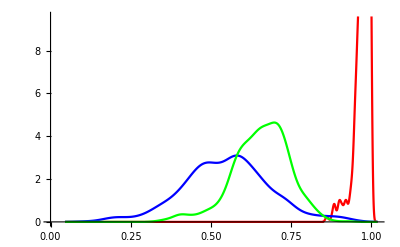

```mathematica
SmoothHistogram[{DeleteCases[Flatten[nrGCM],0.],DeleteCases[Flatten[nrObser],0.],DeleteCases[Flatten[nrSimu],0.]},
PlotStyle->{Red,Blue,Green}]
```

```mathematica
color[x_]:=Rcolorfunction[x,0.3,.9];
plot[nrGCM,plat4GCM,plon4GCM]
plot[nrObser,plat4GCM,plon4GCM]
plot[nrSimu,plat4GCM,plon4GCM]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Correlation[Flatten[Mean[validation[[;;,"P_GCM"]]][[1]]],Flatten[Mean[validation[[;;,"P_Obser"]]][[1]]]]
Correlation[Flatten[Mean[simuObser][[1]]],Flatten[Mean[validation[[;;,"P_Obser"]]][[1]]]]
(*Correlation[Flatten[Mean[simuObser][[1]]],Flatten[Mean[validation[[;;,"P_GCM"]]][[1]]]]*)

Correlation[Flatten[Variance[validation[[;;,"P_GCM"]]][[1]]],Flatten[Variance[validation[[;;,"P_Obser"]]][[1]]]]
Correlation[Flatten[Variance[simuObser][[1]]],Flatten[Variance[validation[[;;,"P_Obser"]]][[1]]]]
(*Correlation[Flatten[Variance[simuObser][[1]]],Flatten[Variance[validation[[;;,"P_GCM"]]][[1]]]]*)
```

0.968045

0.975142

0.96849

0.983263

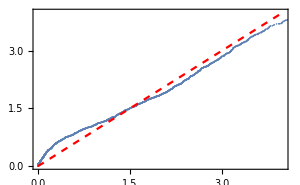
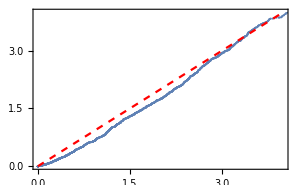

```mathematica
i=7;j=32;
Labeled[Show[{ListPlot[Transpose[{Sort[validation[[;;,"P_Obser"]][[;;,1,i,j]]],Sort[validation[[;;,"P_GCM"]][[;;,1,i,j]]]}],
PlotRange->{{0,4},{0,4}},Frame->True],Plot[x,{x,0,4},PlotStyle->{Red,Dashed}]},ImageSize->300],
Show[{ListPlot[Transpose[{Sort[validation[[;;,"P_Obser"]][[;;,1,i,j]]],Sort[simuObser[[;;,1,i,j]]]}],
PlotRange->{{0,4},{0,4}},Frame->True],Plot[x,{x,0,4},PlotStyle->{Red,Dashed}]},ImageSize->300],Right]
```

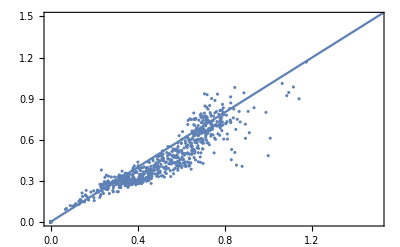

```mathematica
Show[{ListPlot[Transpose[{Flatten[Mean[validation[[;;,"P_Obser"]]][[1]]],Flatten[Mean[simuObser][[1]]]}],
		PlotRange->{{0,1.5},{0,1.5}}],
      Plot[x,{x,0,3}]},Frame->True]
```

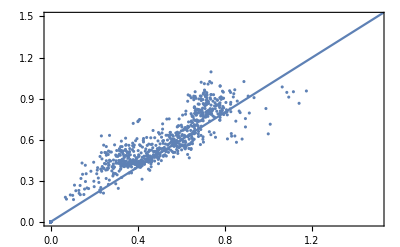

```mathematica
Show[{ListPlot[Transpose[{Flatten[Mean[validation[[;;,"P_Obser"]]][[1]]],Flatten[Mean[validation[[;;,"P_GCM"]]][[1]]]}],
		PlotRange->{{0,1.5},{0,1.5}}],
      Plot[x,{x,0,3}]},Frame->True]
```

```mathematica
Mean[Abs[Flatten[Mean[validation[[;;,"P_Obser"]]][[1]]]-Flatten[Mean[simuObser][[1]]]]]
Mean[Abs[Flatten[Mean[validation[[;;,"P_Obser"]]][[1]]]-Flatten[Mean[validation[[;;,"P_GCM"]]][[1]]]]]
```

0.0453419

0.056557

```mathematica
Mean[Abs[Flatten[Variance[validation[[;;,"P_Obser"]]][[1]]]-Flatten[Variance[simuObser][[1]]]]]
Mean[Abs[Flatten[Variance[validation[[;;,"P_Obser"]]][[1]]]-Flatten[Variance[validation[[;;,"P_GCM"]]][[1]]]]]
```

0.047492

0.062897

```mathematica
(*simuObser=(simuObser+validation[[;;,"P_GCM"]])/2;*)
```

```mathematica
day=RandomSample[Range[Length[simuObser]]][[1]]
color[x_]:=Rcolorfunction[x,0.01,3];
plot[validation[[day,"P_Obser",1]],plat4GCM,plon4GCM]
plot[validation[[day,"P_GCM",1]],plat4GCM,plon4GCM]
plot[simuObser[[day,1]],plat4GCM,plon4GCM]
```

3683

-Graphics-

-Graphics-

-Graphics-

```mathematica
color[x_]:=Rcolorfunction[x,0.01,4];
plot[Block[{tempt=Quiet[Skewness[simuObser][[1]]]},
	Table[If[validMatrix[[i,j]]==1,tempt[[i,j]],0],{i,26},{j,48}]],plat4GCM,plon4GCM]
plot[Block[{tempt=Quiet[Skewness[validation[[;;,"P_Obser"]]][[1]]]},
	Table[If[validMatrix[[i,j]]==1,tempt[[i,j]],0],{i,26},{j,48}]],plat4GCM,plon4GCM]
plot[Block[{tempt=Quiet[Skewness[validation[[;;,"P_GCM"]]][[1]]]},
	Table[If[validMatrix[[i,j]]==1,tempt[[i,j]],0],{i,26},{j,48}]],plat4GCM,plon4GCM]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
color[x_]:=Rcolorfunction[x,0.01,1.15];
plot[Variance[simuObser][[1]],plat4GCM,plon4GCM]
plot[Variance[validation[[;;,"P_Obser"]]][[1]],plat4GCM,plon4GCM]
plot[Variance[validation[[;;,"P_GCM"]]][[1]],plat4GCM,plon4GCM]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
color[x_]:=Rcolorfunction[x,0.01,.8];
plot[Mean[simuObser][[1]],plat4GCM,plon4GCM]
plot[Mean[validation[[;;,"P_Obser"]]][[1]],plat4GCM,plon4GCM]
plot[Mean[validation[[;;,"P_GCM"]]][[1]],plat4GCM,plon4GCM]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
showCycleGan[trained]
```

GCM | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
GCM_Reconstruct | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Obser_Generated | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Obser | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Obser_Reconstruct | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
GCM_Generated | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(*SetDirectory["/Users/pan11/Documents/CycleGAN/Results/Forecast/"];
years=Range[2009,2015];
{forecast,dates,lat,lon}=Block[{tt},
   tt=Table[Block[{start,data,tempt,d},
   year=years[[i]];
   tempt=Import["forecast_"<>ToString[year]<>".mx"];
   d=tempt[["data"]][[;;,;;,;;,1;;-2]];
   d=Map[Map[Map[#*validMatrix&,#]&,#]&,d];
   d=d/. x_ /; x<0.->0.;
   {d,tempt[["start"]]}],{i,Length[years]}];
   {Flatten[tt[[;;,1]],1],Flatten[tt[[;;,2]],1],
   Import["forecast_2009.mx"]["lat"],Import["forecast_2009.mx"]["lon"]}];
forecast=forecast*24.*3600.;
pObser=Import["Obser.mx"]["data"];
pObser=Flatten[pObser,1];
start=Map[DateDifference[{2008,12,31},#][[1]]&,dates];
verification=Table[pObser[[start[[i]];;start[[i]]+44]],{i,Length[start]}];
verification=verification/. x_ /; x<0.->0.;
verification=verification[[;;,;;,1;;-2]];
verification=Map[Map[#*validMatrix&,#]&,verification];
Export["/Users/pan11/Documents/CycleGAN/Results/Forecast/forecast.mx",
 <|"forecast"->NumericArray[forecast,"Real32"],
   "obser"->NumericArray[verification,"Real32"],
   "dates"->dates|>];*)
```

```mathematica
forecast=Normal[Import["/Users/pan11/Documents/CycleGAN/Results/Forecast/forecast.mx"]["forecast"]];
obser=Normal[Import["/Users/pan11/Documents/CycleGAN/Results/Forecast/forecast.mx"]["obser"]];
mforecast=Map[Mean,forecast];
```

```mathematica
MinMax[forecast]
MinMax[obser]
MinMax[mforecast]
```

{0.,360.577}

{0.,217.478}

{0.,114.908}

```mathematica
Dimensions[forecast]
Dimensions[obser]
Dimensions[mforecast]
```

{359,10,45,26,48}

{359,45,26,48}

{359,45,26,48}

```mathematica
Dimensions[forecast]
```

{359,10,45,26,48}

```mathematica
sforecast=Block[{models,data},
	data=Map[Map[Map[List,#]&,#]&,Log[forecast+1.]];
	SetDirectory["/Users/pan11/Documents/CycleGAN/Results/Trained"];
	models=Map[Import[#][["Generator_GCM->Obser"]]&,FileNames["*Step_2*mx"]];
	Table[Block[{tempt=models[[i]]},
	Table[tempt[data[[date,member,lead]]],{date,Length[data]},{member,Dimensions[data][[2]]},
										  {lead,(*Dimensions[data][[3]]*)7}]],{i,Length[models]}]];
```

```mathematica
Dimensions[sforecast]
```

{22,359,10,7,1,26,48}

```mathematica
msforecast=Mean[sforecast];
msforecast=Map[Mean,msforecast];
msforecast=msforecast[[;;,;;,1]];
```

```mathematica
Dimensions[sforecast]
```

{22,359,10,7,1,26,48}

```mathematica
nmsforecast=Mean[(Exp[sforecast]-1.)];
nmsforecast=Map[Mean,nmsforecast];
nmsforecast=nmsforecast[[;;,;;,1]];
```

```mathematica
Dimensions[nmsforecast]
```

{359,7,26,48}

```mathematica
MinMax[msforecast]
MinMax[nmsforecast]
MinMax[obser]
MinMax[mforecast]
```

{0.,5.18201}

{0.,456.082}

{0.,217.478}

{0.,114.908}

```mathematica
Dimensions[mforecast]
Dimensions[msforecast]
```

{359,45,26,48}

{359,7,26,48}

```mathematica
corrRaw=Table[If[And[validMatrix[[i,j]]==1,Variance[obser[[;;,lead,i,j]]]≠-0.,Variance[mforecast[[;;,lead,i,j]]]≠0],
	Correlation[obser[[;;,lead,i,j]],mforecast[[;;,lead,i,j]]],0],{lead,2,7},{i,26},{j,48}];
```

```mathematica
corrRaw=Table[If[And[(*validMatrix[[i,j]]==1,*)Variance[obser[[;;,lead,i,j]]]≠-0.,Variance[rawForecast[[;;,lead,i,j]]]≠0],
	Correlation[obser[[;;,lead,i,j]],rawForecast[[;;,lead,i,j]]],0],{lead,2,7},{i,26},{j,48}];
```

```mathematica
corrCorrect=Table[If[And[(*validMatrix[[i,j]]==1,*)Variance[obser[[;;,lead,i,j]]]≠-0.,Variance[msforecast[[;;,lead,i,j]]]≠0],
	Correlation[obser[[;;,lead,i,j]],msforecast[[;;,lead,i,j]]],0],{lead,2,7},{i,26},{j,48}];
```

```mathematica
Map[Mean[Select[Flatten[#],Positive]]&,corrRaw]
```

{0.528192,0.539787,0.528587,0.459629,0.431279,0.379899}

```mathematica
Dimensions[corrRaw]
```

{6,26,48}

```mathematica
(*corr1=Table[If[And[Variance[mforecast[[;;,lead,i,j]]]≠0,Variance[verification[[;;,lead,i,j]]]≠0],
Correlation[mforecast[[;;,lead,i,j]],verification[[;;,lead,i,j]]],0],{lead,45},{i,26},{j,48}];*)

(*corr2=Table[If[And[Variance[mforecast[[;;,lead,i,j]]]≠0,Variance[(verification[[;;,lead,i,j]]+verification[[;;,lead+1,i,j]])/2.]≠0],
Correlation[mforecast[[;;,lead,i,j]],(verification[[;;,lead,i,j]]+verification[[;;,lead+1,i,j]])/2.],0],{lead,45},{i,26},{j,48}];*)
```

```mathematica
Map[Mean[Select[Flatten[#],Positive]]&,corrRaw[[1;;6]]]-Map[Mean[Select[Flatten[#],Positive]]&,corrCorrect[[1;;6]]]
```

{-0.0216647,-0.0176795,-0.00613924,-0.0232716,-0.000878962,0.00331518}

```mathematica
{rmseRaw,rmseNew}=Import["/Users/pan11/rmse.mx"];
```

```mathematica
color[x_]:=Rcolorfunction[x,0,5];
lead=1;
plot[rmseNew[[1]],plat4GCM,plon4GCM]
plot[rmseRaw[[1]],plat4GCM,plon4GCM]
```

-Graphics-

-Graphics-

```mathematica
DateDifference[{1948,1,1},{1999,12,31}][[1]]/DateDifference[{1948,1,1},{2006,12,31}][[1]]+0.
```

0.88134

```mathematica
NetInitialize[Cycles,All]
```

NetInitialize::arg1: First argument to NetInitialize should be a net or list of nets.

NetInitialize[Cycles,All]

```mathematica
DateDifference[{1948,1,1},{2006,12,31}][[1]]
```

21549

```mathematica
166.5W - 125.5W
```

```mathematica
Round[RandomReal[{-1,1},10],0.001]
```

{-0.123,0.302,0.781,-0.038,0.381,-0.505,0.916,-0.615,-0.407,0.084}

```mathematica
{234,294}-360.
```

{-126.,-66.}

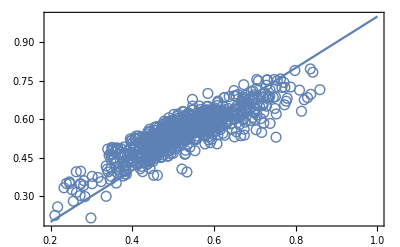
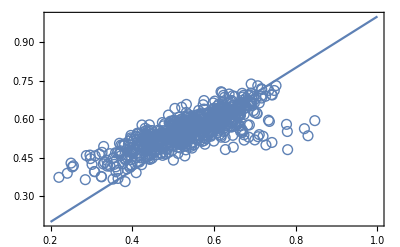
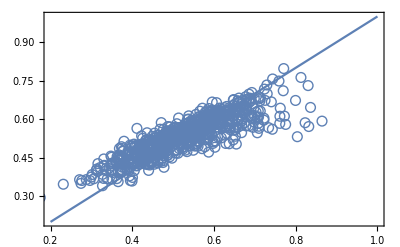
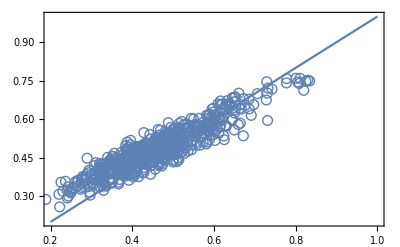
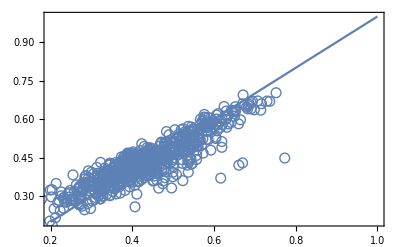
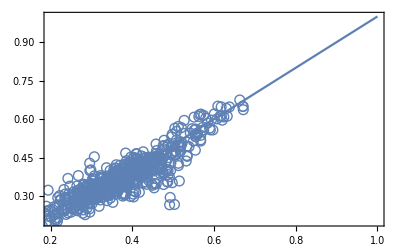

```mathematica
Table[
Show[{ListPlot[Transpose[{Flatten[corrRaw[[lead]]],Flatten[corrCorrect[[lead]]]}],PlotRange->{{0.2,1},{0.2,1}},
	PlotMarkers->Style["○",10]],
	  Plot[x,{x,0.2,1}]},Frame->True],{lead,6}]
```

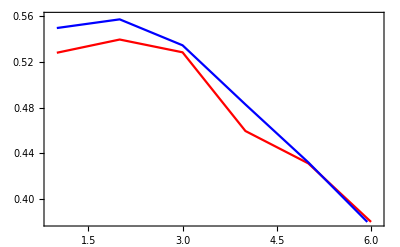

```mathematica
ListLinePlot[{Map[Mean[Select[Flatten[#],Positive]]&,corrRaw[[1;;6]]],
              Map[Mean[Select[Flatten[#],Positive]]&,corrCorrect[[1;;6]]]},PlotStyle->{Red,Blue},
              PlotRange->{{.9,6.1},{0.38,0.56}},Frame->True]
```

```mathematica
corrCorrect=Table[If[And[validMatrix[[i,j]]==1,Variance[obser[[;;,lead,i,j]]]≠-0.,Variance[nmsforecast[[;;,lead,i,j]]]≠0],
	Correlation[obser[[;;,lead,i,j]],nmsforecast[[;;,lead,i,j]]],0],{lead,2,7},{i,26},{j,48}];
```

```mathematica
Map[Mean[Select[Flatten[#],Positive]]&,corrRaw[[1;;6]]]-Map[Mean[Select[Flatten[#],Positive]]&,corrCorrect[[1;;6]]]
```

{-0.00928262,-0.00765373,-0.00883088,-0.00199958,-0.00122715,0.00533809}

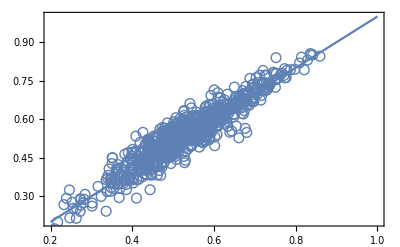
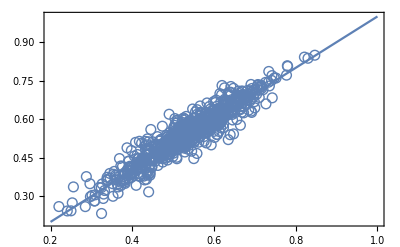
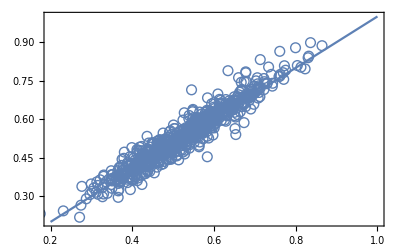
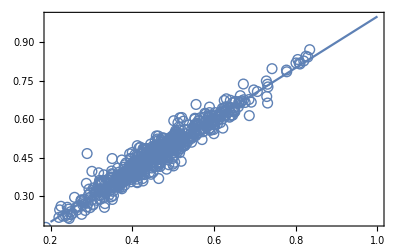
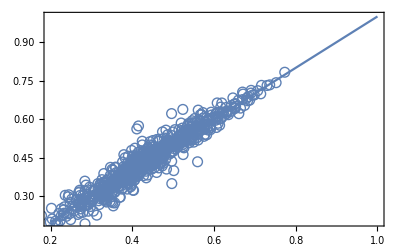
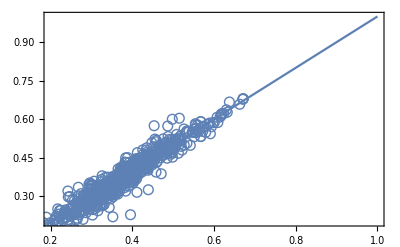

```mathematica
Table[Show[{ListPlot[Transpose[{Flatten[corrRaw[[lead]]],Flatten[corrCorrect[[lead]]]}],PlotRange->{{0.2,1},{0.2,1}},
	PlotMarkers->Style["○",10]],
	  Plot[x,{x,0.2,1}]},Frame->True],{lead,6}]
```

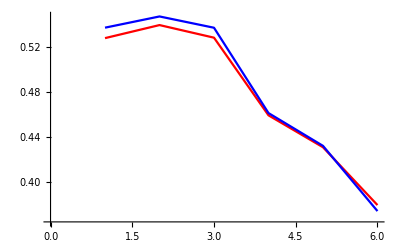

```mathematica
ListLinePlot[{Map[Mean[Select[Flatten[#],Positive]]&,corrRaw[[1;;6]]],
              Map[Mean[Select[Flatten[#],Positive]]&,corrCorrect[[1;;6]]]},PlotStyle->{Red,Blue}]
```

```mathematica
color[x_]:=Rcolorfunction[x,0.2,.8];
lead=1;
plot[corrRaw[[lead]],plat4GCM,plon4GCM]
plot[corrCorrect[[lead]],plat4GCM,plon4GCM]

color[x_]:=Rcolorfunction[x,0.01,0.2];
plot[corrCorrect[[lead]]-corrRaw[[lead]],plat4GCM,plon4GCM]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
(*Export["/usr/workspace/pan11/CycleGAN/Forecast/final.mx",
<|"forecast"->forecast,"obser"->verification,"dates"->start|>];*)
```

## Support

```mathematica
Rcolorfunction[y_,min_,max_]:=Block[{spectrum},
	spectrum[z_]:=Blend[{Blend[{Lighter[Lighter[Cyan]],White}],Lighter[Cyan],Cyan,(*Blend[{Cyan,Lighter[Green]}],*)Lighter[Green],
			             Blend[{Lighter[Green],Yellow}],Yellow,Blend[{Yellow,Orange}],
			             (*Blend[{Darker[Yellow],Orange}],*)Lighter[Orange],
			             Orange,Blend[{Orange,Red}],Lighter[Red],Red(*,Darker[Darker[Red]],
			             Blend[{Darker[Red],Black}],
			             Blend[{Darker[Darker[Red]],Black}]*)},(z-min)/(max-min)];
	Piecewise[{{White,y<min},{Darker[Red],y>=max},{spectrum[y],y≥min}}]]
```

```mathematica
(* WESN define the box, [j,i]tspacing -> major and minor tick spacing *)
CJAGetLatitudeTicks[w_, e_, s_, n_, jtspacing_:2, itspacing_:0.25, ticklength_:0.0] := 
  Module[{left, right, i},
  left = Join[
    Table[{N[GeoGridPosition[GeoPosition[{i, w}], "Mercator"]][[1]][[2]], If[i>0,ToString[i]<>".baN",If[i==0,"0.ba ",ToString[-i]<>".baS"]], {ticklength, 0.0}},
        {i, s, n, jtspacing}],
    Table[{N[GeoGridPosition[GeoPosition[{i, w}], "Mercator"]][[1]][[2]], "", {ticklength/2, 0.0}},
        {i, s, n, itspacing}]
    ];
  
  right = Join[
    Table[{N[GeoGridPosition[GeoPosition[{i, e}], "Mercator"]][[1]][[2]], "",{ticklength, 0.0}},
         {i, s, n, jtspacing}],
    Table[{N[GeoGridPosition[GeoPosition[{i, e}], "Mercator"]][[1]][[2]], "",{ticklength/2, 0.0}}, 
          {i, s, n, itspacing}]
    ];
  
  {left, right}
  ]
(**)
CJAGetLongitudeTicks[w_, e_, s_, n_, jtspacing_:5, itspacing_:0.25, ticklength_:0.0] := 
Module[{bottom, top, i},
  bottom = Join[
    Table[{N[GeoGridPosition[GeoPosition[{s, i}], "Mercator"]][[1]][[1]], 
    If[Or[i==360,i==0],"0.ba ",If[i>180,ToString[360-i]<>".baW",If[i<0,ToString[-i]<>".baW",If[i==180,ToString[i]<>".ba ",ToString[i]<>".baE"]]]], {ticklength, 0.0}}, 
       {i, w, e, jtspacing}],
    Table[{N[GeoGridPosition[GeoPosition[{s, i}], "Mercator"]][[1]][[1]], "", {ticklength/2, 0.0}}, 
        {i, w, e, itspacing}]
    ];
  
  top = Join[
    Table[{N[GeoGridPosition[GeoPosition[{n, i}], "Mercator"]][[1]][[1]], "", {ticklength, 0.0}},
         {i, w, e, jtspacing}],
    Table[{N[GeoGridPosition[GeoPosition[{n, i}], "Mercator"]][[1]][[1]], "", {ticklength/2, 0.0}},
         {i, w, e, itspacing}]
    ];
  
  {bottom, top}
  ]
```

```mathematica
latTicks = Block[{tempt=CJAGetLatitudeTicks[-25, 335, -62, 62],position},
	position=Position[Map[StringSplit[#,".ba"]&,tempt[[1]][[;;,2]]],_?(And[Length[#]>1,Mod[ToExpression[#[[1]]],4]==0]&)][[;;,1]];
	tempt[[;;,position]]];
	
lonTicks = Block[{tempt=CJAGetLongitudeTicks[-25, 335, -62, 62],position},
	position=Position[Map[StringSplit[#,".ba"]&,tempt[[1]][[;;,2]]],_?(And[Length[#]>1,Mod[Abs[ToExpression[#[[1]]]],10]==0]&)][[;;,1]];
	tempt[[;;,position]]];
```

```mathematica
plot[data_,lat_,lon_]:=Block[{background},
	background=Rasterize[MatrixPlot[Reverse[data],Frame->False,PlotRangePadding->None,PlotLegends->None,
		ColorFunctionScaling->False,
		ColorFunction->color],RasterSize->1000];
	GeoGraphics[{FaceForm[None],EdgeForm[Black],LinguisticAssistant["Polygon"]},
	GeoRange->{MinMax[lat]+{-.25,.25},MinMax[lon]},
	ImageSize->300,
	GeoRangePadding->None,
	GeoProjection->"Mercator",
	Frame->True,
	FrameTicks->{latTicks, lonTicks},
	BaseStyle->{FontFamily->"Arial",10,Black},
	(*ImagePadding->{{50,1},{25,35}},*)
	GeoBackground->GeoStyling[{"GeoImage",background}]]]
```